```mathematica
xList = π*{0,1/6,1/4,1/3,1/2};
xList2 = {π/12,(5π)/12,(7π)/24};
func[x_]:=Sin[x];
```

```mathematica
L[func_,x_,deg_,fst_:0]:=Return[Expand@N@(1/(xList[[fst+deg+1]]-xList[[fst+1]]))*If[deg==1,
Det[{func[xList[[fst+1;;fst+1+deg]]],xList[[{fst+1,fst+1+deg}]]-x}],
Det[{{L[func,x,deg-1,fst],L[func,x,deg-1,fst+1]},xList[[{fst+1,fst+1+deg}]]-x}]]]
```

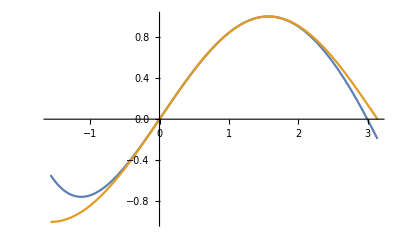

```mathematica
Plot[{Expand@L[func,x,4],func[x]},{x,-π/2,π}]
```

### общий вид таблицы

```mathematica
matr1=Transpose[{"x"<>ToString@#&/@Range[0,Length[xList]-1],
"y"<>ToString@#&/@Range[0,Length[xList]-1],
"x"<>ToString@#<>"-x"&/@Range[0,Length[xList]-1],
Sequence@@Array[""&,{Length[xList]-1,Length[xList]}]
}];
```

```mathematica
matr2=Transpose[{xList,
N@func@xList,
xList-x,
Sequence@@Array[""&,{Length[xList]-1,Length[xList]}]
}]
```

{{0,0.,-x,,,,},{π/6,0.5,π/6-x,,,,},{π/4,0.707107,π/4-x,,,,},{π/3,0.866025,π/3-x,,,,},{π/2,1.,π/2-x,,,,}}

```mathematica
Table[Set[matr1[[fst+deg+1,deg+3]],Expand@N@L[func,x,deg,fst]],{deg,1,Length[xList]-1},{fst,0,Length[xList]-1-deg}];
Table[Set[matr2[[fst+deg+1,deg+3]],Expand@N@L[func,x,deg,fst]],{deg,1,Length[xList]-1},{fst,0,Length[xList]-1-deg}];
```

```mathematica
gridMatr1=Grid[matr1,Frame->All];
gridMatr2=Grid[matr2,Frame->All];
```

```mathematica
gridMatr1
gridMatr2
```

x0 | y0 | x0-x |  |  |  | 
x1 | y1 | x1-x | 0.95493 x |  |  | 
x2 | y2 | x2-x | 0.0857864+0.79109 x | 1.06416 x-0.208608 x^2 |  | 
x3 | y3 | x3-x | 0.230351+0.607024 x | -0.058778+1.25125 x-0.351539 x^2 | 1.00803 x-0.0299438 x^2-0.136489 x^3 | 
x4 | y4 | x4-x | 0.598076+0.255873 x | -0.137374+1.42638 x-0.4471 x^2 | -0.0194799+1.08864 x-0.136525 x^2-0.0912547 x^3 | 0.995626 x+0.021373 x^2-0.204341 x^3+0.0287971 x^4

0 | 0. | -x |  |  |  | 
π/6 | 0.5 | π/6-x | 0.95493 x |  |  | 
π/4 | 0.707107 | π/4-x | 0.0857864+0.79109 x | 1.06416 x-0.208608 x^2 |  | 
π/3 | 0.866025 | π/3-x | 0.230351+0.607024 x | -0.058778+1.25125 x-0.351539 x^2 | 1.00803 x-0.0299438 x^2-0.136489 x^3 | 
π/2 | 1. | π/2-x | 0.598076+0.255873 x | -0.137374+1.42638 x-0.4471 x^2 | -0.0194799+1.08864 x-0.136525 x^2-0.0912547 x^3 | 0.995626 x+0.021373 x^2-0.204341 x^3+0.0287971 x^4

### π/12

```mathematica
N@Grid[matr2/.x->xList2[[1]],Frame->All]
```

0. | 0. | -0.261799 |  |  |  | 
0.523599 | 0.5 | 0.261799 | 0.25 |  |  | 
0.785398 | 0.707107 | 0.523599 | 0.292893 | 0.264298 |  | 
1.0472 | 0.866025 | 0.785398 | 0.38927 | 0.244705 | 0.2594 | 
1.5708 | 1. | 1.309 | 0.665064 | 0.205407 | 0.25453 | 0.258588

### (5π)/12

```mathematica
N@Grid[matr2/.x->xList2[[2]],Frame->All]
```

0. | 0. | -1.309 |  |  |  | 
0.523599 | 0.5 | -0.785398 | 1.25 |  |  | 
0.785398 | 0.707107 | -0.523599 | 1.12132 | 1.03553 |  | 
1.0472 | 0.866025 | -0.261799 | 1.02494 | 0.976756 | 0.962061 | 
1.5708 | 1. | 0.261799 | 0.933013 | 0.963656 | 0.966931 | 0.96612

### (7π)/24

```mathematica
N@Grid[matr2/.x->xList2[[3]],Frame->All]
```

0. | 0. | -0.916298 |  |  |  | 
0.523599 | 0.5 | -0.392699 | 0.875 |  |  | 
0.785398 | 0.707107 | -0.1309 | 0.81066 | 0.799937 |  | 
1.0472 | 0.866025 | 0.1309 | 0.786566 | 0.79259 | 0.793508 | 
1.5708 | 1. | 0.654498 | 0.832532 | 0.794227 | 0.793204 | 0.79333

### погрешности

```mathematica
a = L[func,#,4]&/@xList2;
b = N@func[xList2];
```

```mathematica
Abs[a-b]
```

{0.000231136,0.000193837,0.000022872}